# Logo interpreter

```mathematica
consumeToSpace[s_]:=With[{p=StringPosition[s," "]},
If[p==={},{s,""},{StringTake[s,1;;p[[1,1]]-1],StringTake[s,p[[1,1]]+1;;]}]
]
```

```mathematica
tokenize[s_]:=First@FixedPoint[With[{ans=consumeToSpace[#[[2]]]},{If[ans[[1]]=!="",Join[#[[1]],{ans[[1]]}],#[[1]]],ans[[2]]}]&,{{},s}]
```

```mathematica
peelOneInstruction[]={};
peelOneInstruction[{}]={};
peelOneInstruction[s_List]:=
Switch[First@s,
"fd",{MoveForward@FromDigits[s[[2]]],s[[3;;]]},
"bk",{MoveBackward@FromDigits[s[[2]]],s[[3;;]]},
"lt",{LeftTurn@FromDigits[s[[2]]],s[[3;;]]},
"rt",{RightTurn@FromDigits[s[[2]]],s[[3;;]]},
"setbackground",{SetBackground[FromDigits[s[[2]]]],s[[3;;]]},
"pd",{PenDown,Rest@s},
"pu",{PenUp,Rest@s},
"cs",{ClearScreen,Rest@s},
"set",{SetColour[ToExpression[s[[2]]]],s[[3;;]]}
]
```

```mathematica
instructions[s_]:=First@FixedPoint[If[#[[2]]==={},#,With[{a=peelOneInstruction[#[[2]]]},{Join[#[[1]],{a[[1]]}],a[[2]]}]]&,{{},tokenize@s}]
```

```mathematica
emptyState={Down,90°,{0,0},{},Black};
```

```mathematica
act[ClearScreen,state_]:={state[[1]],state[[2]],state[[3]],{},state[[5]]}
act[LeftTurn[x_],state_]:={state[[1]],state[[2]]+x °,state[[3]],state[[4]],state[[5]]}
act[RightTurn[x_],state_]:={state[[1]],state[[2]]-x °,state[[3]],state[[4]],state[[5]]}
act[MoveForward[x_],state_]:=With[{newEnd={x Cos[state[[2]]],x Sin[state[[2]]]}+state[[3]]},{state[[1]],state[[2]],newEnd,
Join[state[[4]],{If[state[[1]]===Down,Opacity[1],Opacity[0]],state[[5]],Line@{state[[3]],newEnd}}],state[[5]]}]
act[MoveBackward[x_],state_]:=act[MoveForward[-x],state]
act[PenDown,state_]:={Down,state[[2]],state[[3]],state[[4]],state[[5]]}
act[PenUp,state_]:={Up,state[[2]],state[[3]],state[[4]],state[[5]]}
act[SetColour[col_],state_]:={state[[1]],state[[2]],state[[3]],state[[4]],col}
act[SetBackground[x_],state_]:=state (*TODO this may need to change *)
```

```mathematica
evaluate[state_,instr_List]:=First@FixedPoint[If[#[[2]]==={},#,{act[#[[2,1]],#[[1]]],Rest@#[[2]]}]&,{state,instr}]
```

Specific property we know holds of the program we are given: it stays within 10 units vertically of its starting point.

```mathematica
isOk[state_]:=AllTrue[First/@First/@state[[4]][[3;;-1;;3]],Abs[#[[2]]]≤10&]
```

```mathematica
display[state_]:=Graphics[Join[state[[4]],{Blue,Disk[state[[3]],1],Red,Arrow[{state[[3]],{state[[3,1]]+Cos[state[[2]]],state[[3,2]]+Sin[state[[2]]]}}]}],PlotRange->{{-100,100},{-10,10}},Background->Black]
display[None]=None;
```

```mathematica
allRaw={
"cs setbackground 0 set Blue pd rt 30 fd 10 bk 10 lt 120 fd 10 lt 60 pu fd 10",
"bk 10 rt 60 fd 10 lt 120 fd 20 rt 120 pu fd 10 pd lt 120 fd 10 rt 60",
"fd 10 pd rt 60 fd 20 set Cyan lt 120 fd 20 rt 60 pu fd 20 pd rt 120 fd 10 bk 10",
"fd 10 pu fd 10 pd fd 10 rt 60 fd 10 rt 120 fd 10 rt 60 fd 10 rt 120 pu fd 20",
"lt 60 fd 10 pu bk 20 set Pink pd fd 10 rt 60 pu fd 20 pd lt 60 fd 10 rt 60 pu",
"pd bk 10 lt 60 pu fd 20 pd rt 60 fd 10 lt 60 pu bk 10 pd rt 60 bk 10 fd 10 set White",
"pd fd 10 pu fd 10 pd fd 10 bk 10 lt 60 fd 10 lt 120 pu fd 20 pd fd 10 pu bk 50",
"pd fd 10 rt 60 pu fd 10 pd rt 60 fd 20 bk 10 lt 60 bk 10 pu fd 20 pd fd 10",
"pd lt 120 fd 10 pu fd 40 pd lt 120 fd 20 rt 120 pu fd 40 pd rt 60 fd 20",
"pu fd 10 rt 60 fd 60 pd fd 10 pu fd 40 pd rt 180 set Cyan fd 20 lt 60 pu fd 10",
"pu fd 20 pd rt 60 fd 10 set Red fd 10 lt 120 fd 10 lt 60 fd 10 bk 10 lt 60",
"rt 120 pu fd 30 pd rt 120 fd 10 bk 10 lt 120 pu fd 70 pd rt 120 set Yellow fd 10",
"rt 60 pu fd 10 pd lt 60 fd 10 rt 60 pu fd 10 pd fd 10 pu fd 20 pd rt 60 fd 10",
"lt 120 pu fd 10 pd fd 10 rt 60 pu fd 30 pd rt 120 fd 20 pu lt 120 fd 40"
};
```

We know `begin` comes first, and `end` comes last; the others are `instrs`.

```mathematica
instrs=instructions/@allRaw[[2;;-2]];
begin=instructions@allRaw[[1]];
end=instructions@allRaw[[-1]];
```

```mathematica
doIt[soFar_]:=With[{output=evaluate[emptyState,Flatten@{begin,Part[instrs,soFar]}]},
If[isOk[output],display@output,None]
]
```

```mathematica
explore[x_?(Length[#]==12&)]=x;
explore[soFar_]:=If[doIt[soFar]===None,None,
With[{upNext=Select[Complement[Range[12],soFar],doIt[Join[soFar,{#}]]=!=None&]},
explore[Join[soFar,{#}]]&/@upNext
]
]
```

Takes a few seconds to evaluate:

```mathematica
allowable=Cases[explore[{}],_List?(#=!={}&&IntegerQ[#[[1]]]&),Infinity];
```

```mathematica
get[perm_]:=With[{output=evaluate[emptyState,Flatten@{begin,Part[instrs,perm],end}]},
If[isOk[output],display@output,None]
]
```

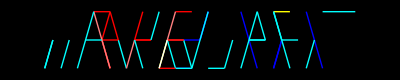
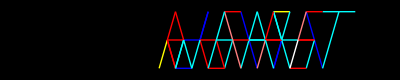
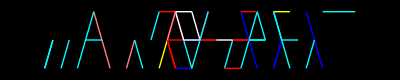
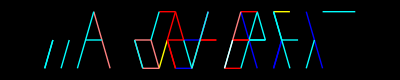
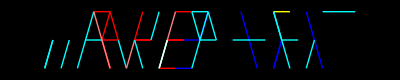
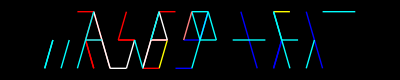
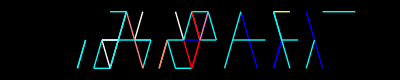
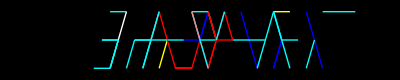

```mathematica
get/@allowable//Column
```

```mathematica
ColorSeparate[Rasterize[%],"RGB"]
```

{-Graphics-,-Graphics-,-Graphics-}

It’s totally the second one:

```mathematica
ColorSeparate[get[allowable[[2]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

“Roffe”, “inhabit”, and something else that I was called away before we could interpret.